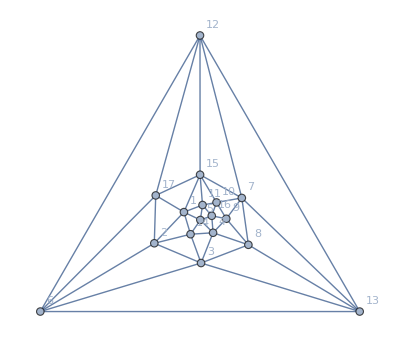

```mathematica
plantri8
```

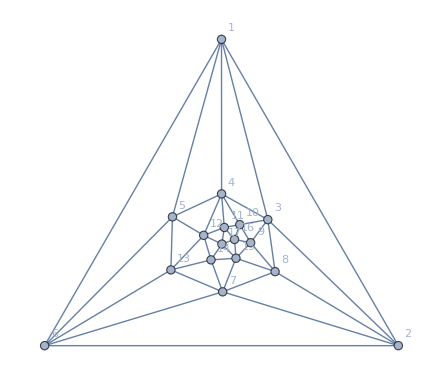

```mathematica
pl8=Graph[plantri[[8]],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
ChromaticPolynomial[pl8,4]/24
```

22

```mathematica
ChromaticPolynomial[pl8,x]//CompleteBaseCoeff
```

{0,0,0,0,22,36281,1796800,17198421,55339513,78241812,56479726,22766977,5401613,773706,66900,3380,91,1}

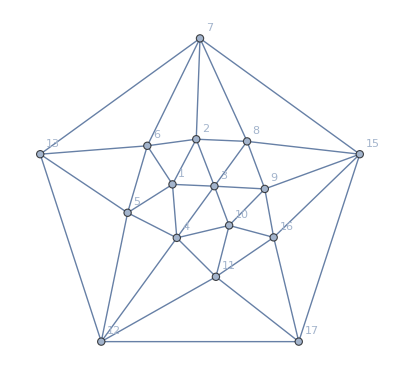

```mathematica
pl8Min=VertexDelete[pl8,14]
```

```mathematica
ApplyAtom[g_,atomKey_,vertices_]:=Block[{result},
result=
]
```

```mathematica
(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])
```

{36166,36112,36085,31738,31714,31711,29608,29605,29551,29527,29524}

```mathematica
Table[FindFullFormula4[EmbedGraphInPlantri8[allGraphs5,atom]],{atom,(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])}]//Flatten//Length
```

63

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,atom],x],{atom,(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])}]//Total//CompleteBaseCoeff
```

{0,0,0,0,63,31366,906909,5851378,13552503,14251874,7761732,2362156,417968,43395,2575,80,1}

```mathematica
ChromaticPolynomial[pl8Min,x]//CompleteBaseCoeff
```

{0,0,0,0,63,31366,906909,5851378,13552503,14251874,7761732,2362156,417968,43395,2575,80,1}

```mathematica
Intersection[FindFullFormula4[pl8Min],Table[FindFullFormula4[EmbedGraphInPlantri8[allGraphs5,atom]],{atom,(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])}]//Flatten]
```

{}

```mathematica
a1=FindFullFormula4[pl8Min]//Sort
```

{v179bx24dfx36cgx58ah,v179bx24dgx36cfx58ah,v179bx25afx36cgx48dh,v179bx25ahx36cfx48dg,v179cx24dgx35bfx68ah,v179cx24dgx36bfx58ah,v179cx25ahx36bfx48dg,v179cx25ahx3bdfx468g,v179cx2adhx35bfx468g,v179hx24dgx35bfx68ac,v17acx249dhx35bfx68g,v17acx249dhx36bfx58g,v17acx259hx36bfx48dg,v17acx259hx3bdfx468g,v17acx29dhx35bfx468g,v17ahx249dx35bfx68cg,v17ahx259bx36cfx48dg,v17ax249dhx35bfx68cg,v17cgx249dhx35bfx68a,v17cgx249dhx36bfx58a,v17cgx249dx35bfx68ah,v17cgx249dx36bfx58ah,v17gx249dhx35bfx68ac,v18acx249dhx357gx6bf,v18acx249dhx36bfx57g,v18acx24dgx36bfx579h,v18acx2bdfx357gx469h,v18adhx24fx36cgx579b,v18adhx24gx36cfx579b,v18adhx259bx36cfx47g,v18adhx259bx37cgx46f,v18adhx25bfx36cgx479,v18adhx25bfx37cgx469,v18adx25bfx36cgx479h,v18adx25bfx37cgx469h,v18ahx24dfx36cgx579b,v18ahx24dgx36cfx579b,v18bdx249hx357gx6acf,v18bdx25afx36cgx479h,v18bdx25afx37cgx469h,v18bdx2acfx357gx469h,v18bx249dhx357gx6acf,v18cgx249dhx357bx6af,v18cgx249dhx36bfx57a,v18cgx249dx36bfx57ah,v18cgx2adfx357bx469h,v18dgx249hx357bx6acf,v18dgx2acfx357bx469h,v18gx249dhx357bx6acf,v19bdx25afx37cgx468h,v19bdx2acfx357gx468h,v19bdx2acfx357hx468g,v19dhx2acfx357bx468g,v1acfx249dhx357bx68g,v1acfx249dhx357gx68b,v1acfx29bdx357gx468h,v1acfx29bdx357hx468g,v1acfx29dhx357bx468g,v1adfx249hx357bx68cg,v1adfx259bx37cgx468h,v1afx249dhx357bx68cg,v1bdfx249hx357gx68ac,v1bfx249dhx357gx68ac}

```mathematica
a2=Map[Length[Flatten[SymbolToSets[#]]]&,Flatten[Table[FindFullFormula4[EmbedGraphInPlantri8[allGraphs5,atom]],{atom,(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])}],1]]//Sort
```

{14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15}

```mathematica
Intersection[a1,a2]
```

{}

```mathematica
Table[allGraphs5[atom,"graph"]->FindFullFormula4[EmbedGraphInPlantri8[allGraphs5,atom]],{atom,(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])}]
```

{-Graphics-→{v1adx259bx3cgx468h,v1acx259hx3bdx468g,v19cx25ahx3bdx468g},-Graphics-→{v1cgx249dx36bfx58a,v1cgx249dx35bfx68a,v1acx29dx35bfx468g,v1acx249dx36bfx58g,v1acx249dx35bfx68g,v19cx2adx35bfx468g,v18adx25bfx3cgx469,v18adx259bx3cgx46f},-Graphics-→{v1cgx249dx36bfx58ah,v1cgx249dx35bfx68ah,v1acx259hx36bfx48dg,v19bdx25afx3cgx468h,v19cx25ahx36bfx48dg,v19cx24dgx36bfx58ah,v19cx24dgx35bfx68ah,v18bdx25afx3cgx469h,v18adx25bfx3cgx469h},-Graphics-→{v1acx29dx357bx468g,v1acx249dx357gx68b,v1acx249dx357bx68g,v19dx2acx357bx468g,v18adx259bx36cx47g,v18adx24gx36cx579b,v18bx249dx357gx6ac,v18gx249dx357bx6ac},-Graphics-→{v1acx29bdx357x468g,v17ax259bx36cx48dg,v19bdx2acx357x468g},-Graphics-→{v1acx29bdx357gx468h,v19bdx2acx357gx468h,v18bdx2acx357gx469h,v18dgx2acx357bx469h,v18ahx24dgx36cx579b,v18bdx249hx357gx6ac,v18dgx249hx357bx6ac,v179bx25ahx36cx48dg,v179bx24dgx36cx58ah},-Graphics-→{},-Graphics-→{v1bdx249hx357gx68ac,v1adx249hx357bx68cg,v18acx2bdx357gx469h,v18cgx2adx357bx469h,v18ahx24dx36cgx579b,v179bx24dx36cgx58ah},-Graphics-→{v1bfx249dx357gx68ac,v1afx249dx357bx68cg,v18adx25bfx36cgx479,v18cgx249dx36bfx57a,v18acx249dx36bfx57g,v18adx24fx36cgx579b,v18acx249dx357gx6bf,v18cgx249dx357bx6af,v179bx25afx36cgx48d,v17ax249dx35bfx68cg,v17gx249dx35bfx68ac},-Graphics-→{v17ax249dx35bfx68cg,v179x24dgx35bfx68ac,v18bdx25afx36cgx479,v18adx25bfx36cgx479,v18cgx249dx36bfx57a,v18acx24dgx36bfx579},-Graphics-→{}}

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,atom],x],{atom,alfa1s}]//Total//CompleteBaseCoeff
```

{0,0,0,0,22,8794,168118,732638,1152521,813839,288835,54254,5396,265,5}

```mathematica
ChromaticPolynomial[pl8,x]//CompleteBaseCoeff
```

{0,0,0,0,22,36281,1796800,17198421,55339513,78241812,56479726,22766977,5401613,773706,66900,3380,91,1}

```mathematica
Length[{0,0,0,0,22,36281,1796800,17198421,55339513,78241812,56479726,22766977,5401613,773706,66900,3380,91,1}]
```

18

```mathematica
Table[ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,atom],x],{atom,(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])}]//Total//CompleteBaseCoeff
```

{0,0,0,0,63,31366,906909,5851378,13552503,14251874,7761732,2362156,417968,43395,2575,80,1}

```mathematica
With[{keys=(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])},
MatrixForm[
Table[PadRight[CompleteBaseCoeff[ ChromaticPolynomial[EmbedGraphInPlantri8[allGraphs5,atom],x]],17],{atom,keys}],
TableHeadings->{Table[allGraphs5[k,"graph"],{k,keys}],( ChromaticPolynomial[pl8Min,x]//CompleteBaseCoeff)}
]
]
```

( | 0 | 0 | 0 | 0 | 63 | 31366 | 906909 | 5851378 | 13552503 | 14251874 | 7761732 | 2362156 | 417968 | 43395 | 2575 | 80 | 1
-Graphics- | 0 | 0 | 0 | 0 | 3 | 1657 | 33021 | 145463 | 229683 | 162452 | 57705 | 10845 | 1079 | 53 | 1 | 0 | 0
-Graphics- | 0 | 0 | 0 | 0 | 8 | 1947 | 34494 | 147410 | 230594 | 162613 | 57714 | 10845 | 1079 | 53 | 1 | 0 | 0
-Graphics- | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 8 | 1947 | 34494 | 147410 | 230594 | 162613 | 57714 | 10845 | 1079 | 53 | 1 | 0 | 0
-Graphics- | 0 | 0 | 0 | 0 | 3 | 1657 | 33021 | 145463 | 229683 | 162452 | 57705 | 10845 | 1079 | 53 | 1 | 0 | 0
-Graphics- | 0 | 0 | 0 | 0 | 9 | 3696 | 103438 | 619374 | 1296107 | 1204556 | 566279 | 144444 | 20555 | 1609 | 64 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 0 | 1586 | 33088 | 146892 | 231967 | 163709 | 57997 | 10874 | 1080 | 53 | 1 | 0 | 0
-Graphics- | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 11 | 4136 | 108277 | 634418 | 1315458 | 1216259 | 569804 | 144977 | 20593 | 1610 | 64 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 6 | 3551 | 103568 | 625157 | 1308956 | 1214382 | 569580 | 144968 | 20593 | 1610 | 64 | 1 | 0
-Graphics- | 0 | 0 | 0 | 0 | 0 | 3942 | 216502 | 1995260 | 5874398 | 7383900 | 4631375 | 1584101 | 309683 | 35082 | 2250 | 75 | 1)

```mathematica
Total[Flatten[{3, 8,9,8,3,9,0,6,11,6,0}]]
```

63

```mathematica
∖
```

```mathematica
5*64+2250
```

2570

```mathematica
SymbolToColoring[v1adx259bx3cgx468h]
```

{1→RGBColor[1, 0, 0],10→RGBColor[1, 0, 0],13→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],5→RGBColor[0, 0, 1],9→RGBColor[0, 0, 1],11→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],12→RGBColor[1, 1, 0],16→RGBColor[1, 1, 0],4→RGBColor[0, 1, 0],6→RGBColor[0, 1, 0],8→RGBColor[0, 1, 0],17→RGBColor[0, 1, 0]}

```mathematica
With[{keys=(ListofVars[allGraphs5[lambdaKey,"colofour"]]/.RepKey["C"])},
TableForm[
Table[Map[ColorGraph[pl8Min,SymbolToSets[#]]&,FindFullFormula4[EmbedGraphInPlantri8[allGraphs5,atom]]],{atom,keys}],
TableHeadings->{Table[allGraphs5[k,"graph"],{k,keys}],None},
TableDepth->1
]
]
```